```mathematica
a={{{0,-3},{1,-2},{2,-1},{3,0},{3,-1},{3,-2},{3,-2},{3,-3},{3,-4},{3,-5},{3,-6},{2,-7},{0,-9},{-1,-8},{-2,-7},{0,-7},{1,-8},{2,-9},{4,-7},{5,-6},{5,-5},{5,-4},{5,-3},{5,-2},{5,-1},{5,0},{4,-1},{3,-2},{2,-3},{0,-3}},
{{0,0},{-2,0},{0,2},{2,0.0}}
}
b=a[[1]];
n=Length[b]-1;
center=Sum[b[[i]],{i,1,4}]/4;
dists=Table[Norm[b[[i]]-center],{i,1,4}];
radius=Max[dists];
 
Do[b[[i]]=b[[i]]-center,{i,1,4}];

b30[t_]:=(1-t)^3;
b31[t_]:=3 *(1-t)^2*t ;
b32[t_]:=3*(1-t)*t^2 ;
b33[t_]:=t^3;


bez[b_,t_]:=b[[1]]*b30[t]+ b[[2]] *b31[t] +b[[3]] *b32[t] + b[[4]] *b33[t];

plot[b_]:=(
curveplot = ParametricPlot[bez[b,t],{t,0,1},PlotStyle->{Thick, Red}];
polygon=Graphics[Line[b]];
points = Graphics[{PointSize[Large],Point[b]}];
Show[{polygon, curveplot, points}]);
```

{{{0,-3},{1,-2},{2,-1},{3,0},{3,-1},{3,-2},{3,-2},{3,-3},{3,-4},{3,-5},{3,-6},{2,-7},{0,-9},{-1,-8},{-2,-7},{0,-7},{1,-8},{2,-9},{4,-7},{5,-6},{5,-5},{5,-4},{5,-3},{5,-2},{5,-1},{5,0},{4,-1},{3,-2},{2,-3},{0,-3}},{{0,0},{-2,0},{0,2},{2,0.}}}

Initial Characters

```mathematica
pts = {{0,-3},{1,-2},{2,-1},{3,0},{3,-1},{3,-2},{3,-2},{3,-3},{3,-4},{3,-5},{3,-6},{2,-7},{0,-9},{-1,-8},{-2,-7},{0,-7},{1,-8},{2,-9},{4,-7},{5,-6},{5,-5},{5,-4},{5,-3},{5,-2},{5,-1},{5,0},{4,-1},{3,-2},{2,-3},{0,-3}};
	Graphics[{Green,BSplineCurve[pts],Blue,Line[pts],Red,Point[pts]}]
```

-Graphics-

```mathematica
pts = {{0,-3},{1,-2},{2,-1},{3,0},{3,-1},{3,-2},{3,-2},{3,-3},{3,-4},{3,-5},{3,-6},{2,-7},{0,-9},{-1,-8},{-2,-7},{0,-7},{1,-8},{2,-9},{4,-7},{5,-6},{5,-5},{5,-4},{5,-3},{5,-2},{5,-1},{5,0},{4,-1},{3,-2},{2,-3},{0,-3}};
Graphics[{Thickness[0.1],Green,BSplineCurve[pts],Blue,Line[pts],Red,Point[pts]}]
```

-Graphics-

```mathematica
pts = {{3,3},{4,3},{5,3},{6,3},{7,3},{7,4},{6,4},{5,4},{4,4},{3,4},{2,4},{1,4},{0,4},{0,3},{1,3},{2,3},{3,3},{4,3},{4,3},{4,2},{4,1},{4,0},{4,-1},{2,-2},{0,-3},{0,-2},{0,-1},{1,-2},{2,-3},{3,-5},{4,-7},{5,-8},{5,-8},{3,-7},{2,-5},{1,-3},{0.8,-1.5},{0,-1.5},{0,-2},{1,-2},{3,-1},{3,0},{3,1},{3,2},{3,3}};
Graphics[{BSplineCurve[pts],Yellow,Line[pts],Red,Point[pts]}]
```

-Graphics-

```mathematica
pts = {{3,3},{4,3},{5,3},{6,3},{7,3},{7,4},{6,4},{5,4},{4,4},{3,4},{2,4},{1,4},{0,4},{0,3},{1,3},{2,3},{3,3},{4,3},{4,3},{4,2},{4,1},{4,0},{4,-1},{2,-2},{0,-3},{0,-2},{0,-1},{1,-2},{2,-3},{3,-5},{4,-7},{5,-8},{5,-8},{3,-7},{2,-5},{1,-3},{0.8,-1.5},{0,-1.5},{0,-2},{1,-2},{3,-1},{3,0},{3,1},{3,2},{3,3}};
Graphics[{Thickness[0.1],BSplineCurve[pts],Yellow,Line[pts],Red,Point[pts]}]
```

-Graphics-

Bezier Polygons, curves and control points

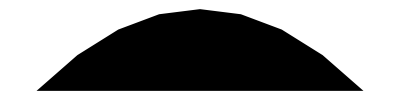

```mathematica
pts = {{-1,0},{0,1},{1,0}};
Graphics[FilledCurve[{BezierCurve[pts]}]]
```

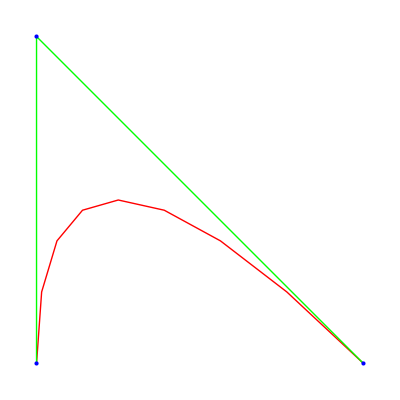

```mathematica
pts = {{0,0},{0,1},{1,0}};
Graphics[{Red,BezierCurve[pts],Green, Line[pts], Blue, Point[pts]}]
```

Curve

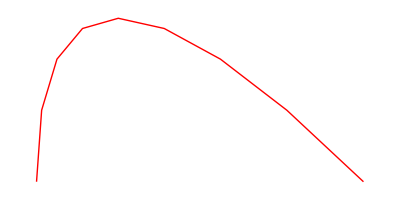

```mathematica
pts = {{0,0},{0,1},{1,0}};
Graphics[{Red,BezierCurve[pts]}]
```

Italic version

```mathematica
a={{0,-3},{1,-2},{2,-1},{3,0},{3,-1},{3,-2},{3,-2},{3,-3},{3,-4},{3,-5},{3,-6},{2,-7},{0,-9},{-1,-8},{-2,-7},{0,-7},{1,-8},{2,-9},{4,-7},{5,-6},{5,-5},{5,-4},{5,-3},{5,-2},{5,-1},{5,0},{4,-1},{3,-2},{2,-3},{0,-3}};
Manipulate[Graphics[{EdgeForm[None],GeometricTransformation[{Red,BSplineCurve[a]},ShearingTransform[t Pi/9,{1,0},{0,1}]]}],{t,0,3},SaveDefinitions->True]
(*use t for check the shear effect*)
```

```mathematica
pts = {{3,3},{4,3},{5,3},{6,3},{7,3},{7,4},{6,4},{5,4},{4,4},{3,4},{2,4},{1,4},{0,4},{0,3},{1,3},{2,3},{3,3},{4,3},{4,3},{4,2},{4,1},{4,0},{4,-1},{2,-2},{0,-3},{0,-2},{0,-1},{1,-2},{2,-3},{3,-5},{4,-7},{5,-8},{5,-8},{3,-7},{2,-5},{1,-3},{0.8,-1.5},{0,-1.5},{0,-2},{1,-2},{3,-1},{3,0},{3,1},{3,2},{3,3}};
Manipulate[Graphics[{EdgeForm[None],GeometricTransformation[{Yellow,BSplineCurve[pts]},ShearingTransform[r Pi/9,{1,0},{0,1}]]}],{r,0,1.5},SaveDefinitions->True]
(*use t for check the shear effect*)
```

A Manipulate environment with a point that moves around the outside curves of one of the characters

```mathematica
der[b_,t_]:=0.33Limit[(bez[b,t+dt]-bez[b,t])/dt,dt->0.0]; 
deriv[b_,t_]:=0.33*(b[[1]]*b30'[t]+ b[[2]] *b31'[t] +b[[3]] *b32'[t] + b[[4]] *b33'[t]);


pointplot[b_,t_]:=Graphics[{PointSize[Large],Yellow,Point[bez[b,t]]}];
derarrowplot[b_,t_]:=Graphics[{Thick,Blue,{Point[{bez[b,t],bez[b,t]+der[b,t]}]}}];

Manipulate[Show[{plot[b],  derarrowplot[b,t], pointplot[b,t]}]
,{t,0,1}]
```

Show::gcomb: Could not combine the graphics objects in Show[{plot[b],derarrowplot[b,0.],pointplot[b,0.]}].